# Working through the chapter Combinatorial Searching in Knuth’s TAOCP

## Exercise 41

For what integers n do we have K_n=P_n? K_n=C_n?




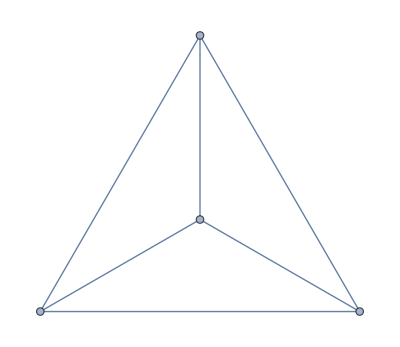

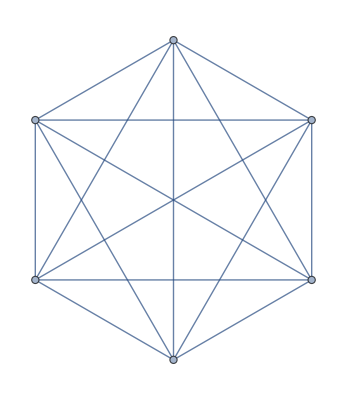
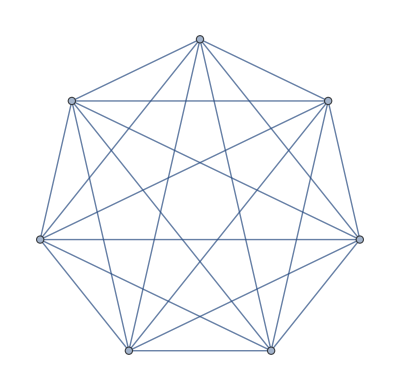
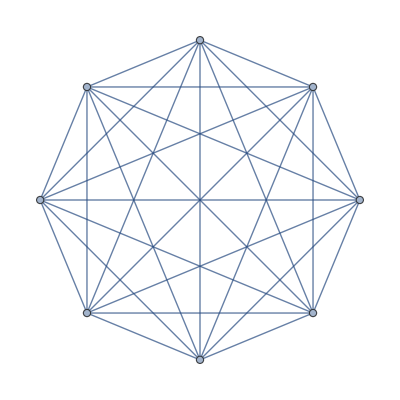
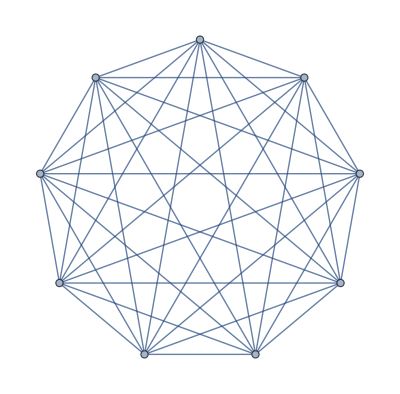

```mathematica
Table[CompleteGraph[i],{i,9}]
```


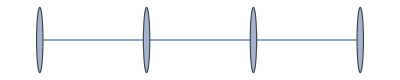
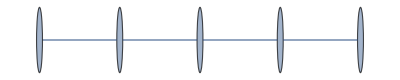
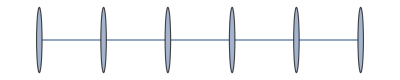
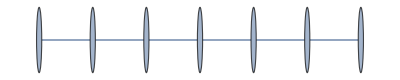
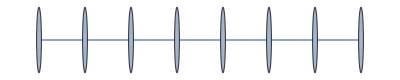
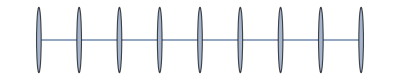
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PathGraph[Range[i]],{i,9}]
```

I’ll use the new isomorphism functionality introduced in recent releases of Mathematica:

```mathematica
FindGraphIsomorphism[-Graphics-,-Graphics-]
```

{<|1→1|>}

```mathematica
Names["*Isom*"]
```

{FindGraphIsomorphism,FindIsomers,FindIsomorphicSubgraph,FindSubgraphIsomorphism,IsomorphicGraphQ,IsomorphicSubgraphQ}

```mathematica
Information/@Names["*Isom*"]
```

{,,,,,}

```mathematica
Select[IsomorphicGraphQ[CompleteGraph[#],PathGraph[Range[#]]]&][Range[10]]
```

{1,2}

```mathematica
Select[IsomorphicGraphQ[CompleteGraph[#],CycleGraph[#]]&][Range[10]]
```

{3}

Donald Knuth lists 0 as an answer as well in addition to 3, but I don’t think the 0 graph exists or makes sense.

## Exercise 43

Are any of the following graphs the same as the Petersen graph?

I have a hard copy edition of the Art of Computer Programming that I am using to answer this exercise.

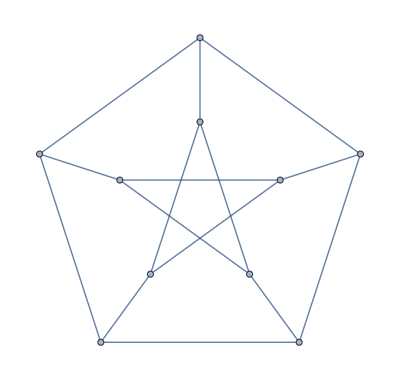

```mathematica
GraphData["PetersenGraph"]
```

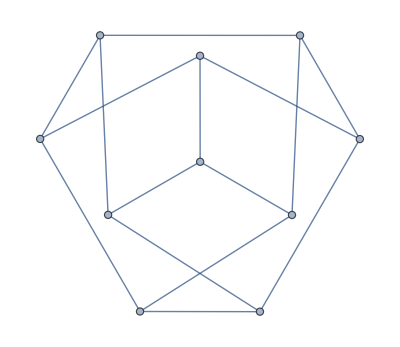

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,1<->5,9<->1,2<->7,3<->10,9<->10,6<->10,4<->8}]
```

```mathematica
IsomorphicGraphQ[Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,1<->5,9<->1,2<->7,3<->10,9<->10,6<->10,4<->8}],GraphData["PetersenGraph"]]
```

True

```mathematica
FindGraphIsomorphism[Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,1<->5,9<->1,2<->7,3<->10,9<->10,6<->10,4<->8}],GraphData["PetersenGraph"]]
```

{<|1→1,2→4,3→2,4→5,5→3,6→8,7→9,8→10,9→6,10→7|>}

```mathematica
GraphData["PetersenGraph","Embeddings"]
```

{{{0.,1.},{-0.951,0.309},{-0.588,-0.809},{0.588,-0.809},{0.951,0.309},{0.,2.},{-1.902,0.618},{-1.176,-1.618},{1.176,-1.618},{1.902,0.618}},{{0.323,0.975},{0.037,0.789},{0.037,0.186},{0.323,0.},{0.5,0.487},{1.287,0.975},{1.,0.789},{1.,0.186},{1.287,0.},{1.464,0.487}},{{0.448354,-0.269958},{0.60481,-0.338987},{0.586329,-0.50903},{0.586329,-0.0309114},{0.862447,-0.50903},{0.724304,-0.131983},{0.724304,-0.269958},{0.843797,-0.338987},{0.862447,-0.0309114},{1.,-0.269958}},{{0.448354,-0.269958},{0.606498,-0.145654},{0.529114,-0.0747932},{0.529114,-0.465148},{0.84211,-0.145654},{1.,-0.269958},{0.919831,-0.0747932},{0.724304,0.00606582},{0.724304,-0.545992},{0.919831,-0.465148}},{{0.454407,-0.222966},{0.632542,-0.53161},{0.549237,-0.0587373},{0.487373,-0.409661},{0.822119,-0.53161},{1.,-0.222966},{0.905932,-0.0587373},{0.727373,0.00609153},{0.727373,-0.271102},{0.967797,-0.409661}},{{0.602252,-0.541848},{0.734705,-0.312345},{0.668478,-0.656599},{0.668478,-0.427096},{0.867236,-0.312345},{1.,-0.541848},{0.93323,-0.656599},{0.801242,-0.656599},{0.801242,-0.503571},{0.93323,-0.427096}},{{0,0},{1,3},{0,4},{1,1},{4,4},{2,0},{2,2},{3,3},{3,1},{4,0}},{{2,2},{6,4},{4,2},{2,4},{6,2},{5,5},{6,6},{4,6},{2,6},{3,5}},{{√(2/(5+√5)),0},{1/2 √(1-2/(√5)),1/2},{-1/2 √(1/10 (5+√5)),1/4 (-1+√5)},{-1/2 √(1/10 (5+√5)),1/4 (1-√5)},{1/2 √(1-2/(√5)),-1/2},{0,√(1/10 (5+√5))},{1/4 (-1-√5),1/2 √(1/10 (5-√5))},{-1/2,-1/2 √(1+2/(√5))},{1/2,-1/2 √(1+2/(√5))},{1/4 (1+√5),1/2 √(1/10 (5-√5))}},{{0.535302,0.95889},{0.328164,0.677274},{0.535302,0.470135},{0.0706049,0.621205},{0.328164,0.262996},{1.,0.621205},{0.742441,0.677274},{0.742441,0.262996},{0.247912,0.0745965},{0.822693,0.0745965}},{{√(5/8-(√5)/8),1/4 (-1-√5)},{0,1},{√(1/2 (5-√5)),1/2 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,2},{-1/2 √(1/2 (5-√5)),1/4 (-1-√5)},{-1/2 √(1/2 (5+√5)),1/4 (-1+√5)},{-√(1/2 (5+√5)),1/2 (-1+√5)},{√(1/2 (5+√5)),1/2 (-1+√5)},{-√(1/2 (5-√5)),1/2 (-1-√5)}}}

```mathematica
Length[GraphData["PetersenGraph","Embeddings"]]
```

11

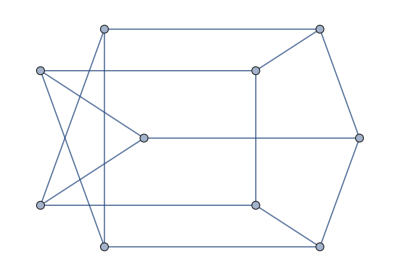
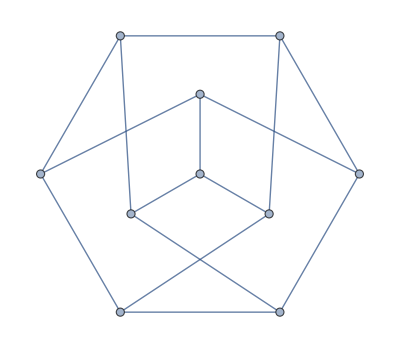
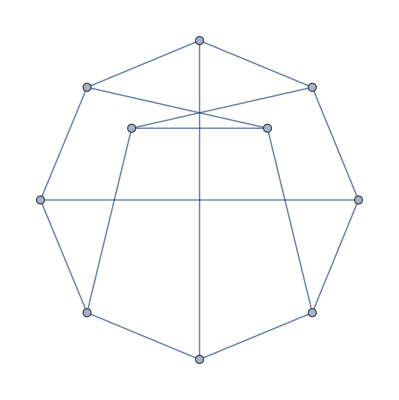
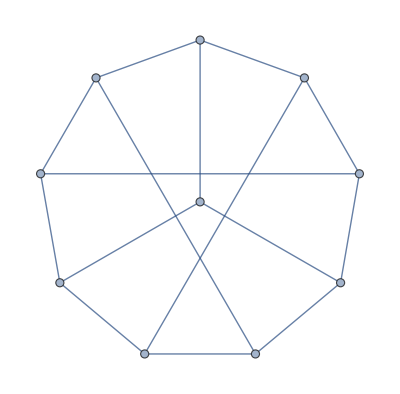
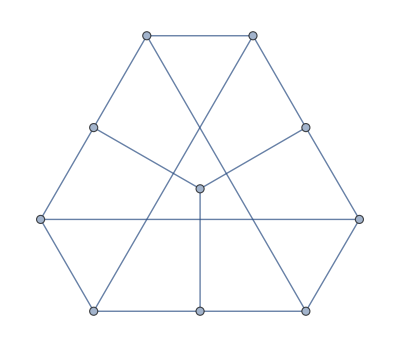
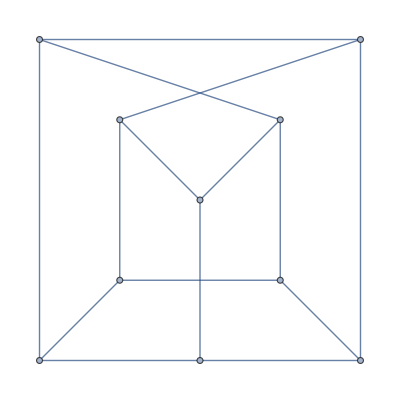
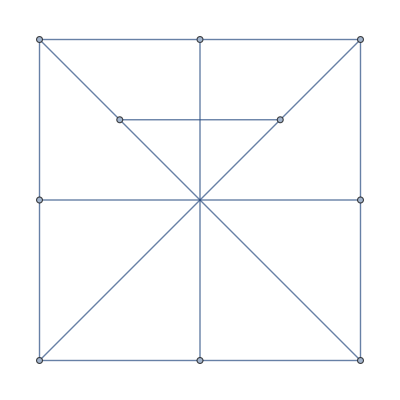
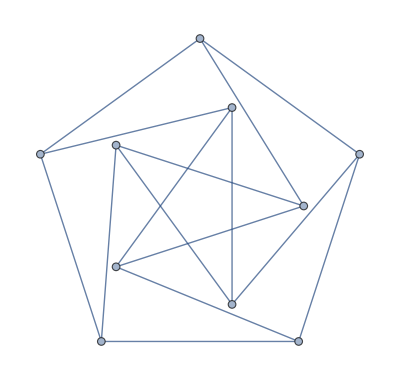
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph[GraphData["PetersenGraph"],VertexCoordinates->#]&/@GraphData["PetersenGraph","Embeddings"]
```

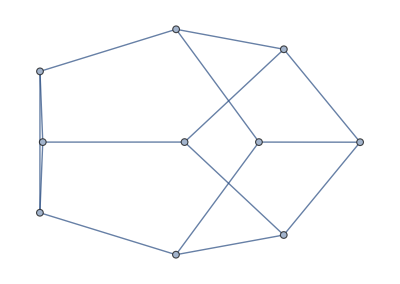

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,1<->7,3<->7,5<->7,2<->8,4<->9,6<->10,8<->9,9<->10,8<->10}]
```

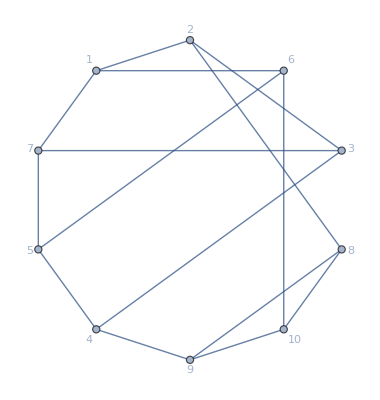

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,1<->7,3<->7,5<->7,2<->8,4<->9,6<->10,8<->9,9<->10,8<->10},GraphLayout->"CircularEmbedding",VertexLabels->Automatic]
```

```mathematica
IsomorphicGraphQ[Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,1<->7,3<->7,5<->7,2<->8,4<->9,6<->10,8<->9,9<->10,8<->10},GraphLayout->"CircularEmbedding",VertexLabels->Automatic],GraphData["PetersenGraph"]]
```

False

```mathematica
FindGraphIsomorphism[GraphData["PetersenGraph"],-Graphics-]
```

{<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>}

```mathematica
FindGraphIsomorphism[GraphData["PetersenGraph"],-Graphics-]
```

```mathematica
FindGraphIsomorphism[GraphData["PetersenGraph"],-Graphics-]
```

{<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>}

```mathematica
FindGraphIsomorphism[-Graphics-,GraphData["PetersenGraph"]]
```

{<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>}

## Exercise 44

How many symmetries does Chvàtal’s graph have?

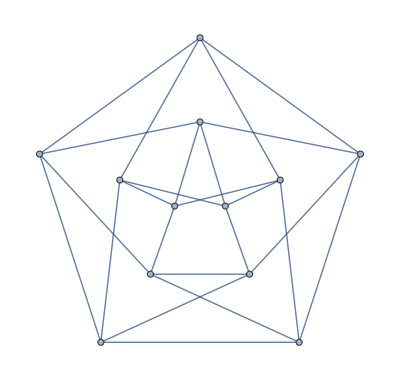

```mathematica
GraphData["ChvatalGraph"]
```

```mathematica
GraphData["ChvatalGraph","AutomorphismCount"]
```

8

There are 8 symmetries.

## Exercise 45

Find an easy way to 4-color the planar graph (17). Would 3 colors suffice?

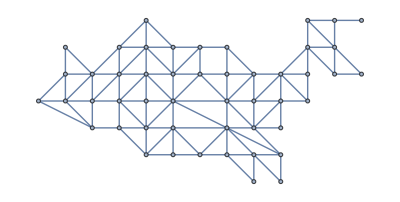

```mathematica
GraphData["ContiguousUSAGraph"]
```

```mathematica
VertexCount[GraphData["ContiguousUSAGraph"]]
```

49

```mathematica
GraphData["ContiguousUSAGraph","ChromaticNumber"]
```

4

The minimum number of colors possible is 4.

```mathematica
FindVertexColoring[GraphData["ContiguousUSAGraph"]]
```

{3,1,2,2,1,3,1,2,1,2,2,4,3,3,1,1,2,3,1,3,3,2,1,1,1,3,2,1,3,2,3,1,3,1,1,2,2,2,1,3,2,3,1,4,1,1,3,2,3}

I can use a resource function I created to color a graph:

```mathematica
ResourceSearch["*color*graph*"]
```

```mathematica
PersistResourceFunction[{"ColorGraphVertices"}]
```

{Success[…]}

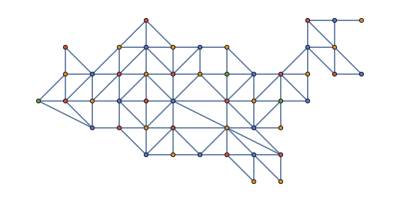

```mathematica
ColorGraphVertices[GraphData["ContiguousUSAGraph"]]
```

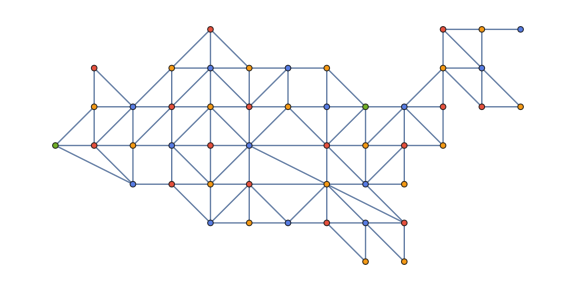

```mathematica
ColorGraphVertices[GraphData["ContiguousUSAGraph"],ImageSize->Large]
```

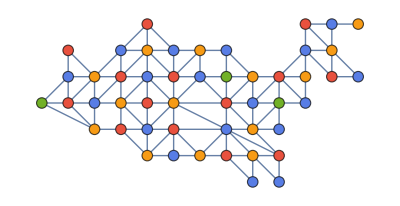

```mathematica
ColorGraphVertices[GraphData["ContiguousUSAGraph"],ImageSize->Full,VertexSize->Large]
```

## Exercise 46

Let G with a graph with n>=3 vertices, defined by a planar diagram that is “maximal,” in the sense that no additional lines can be drawn between nonadjacent vertices without crossing an existing edge.

The graph data property I am looking for is “Triangulated” or “maximally planar”.

```mathematica
GraphData["Triangulated"]
```

{{Apollonian,2},{Apollonian,3},{Apollonian,4},{Apollonian,5},{Apollonian,6},{ChromaticallyEquivalent,{11,1,1}},{ChromaticallyEquivalent,{11,1,2}},{ChromaticallyEquivalent,{11,2,1}},{ChromaticallyEquivalent,{11,2,2}},{ChromaticallyEquivalent,{11,3,1}},{ChromaticallyEquivalent,{11,3,2}},{ChromaticallyEquivalent,{12,1,1}},{ChromaticallyEquivalent,{12,1,2}},{ChromaticallyEquivalent,{13,1,1}},{ChromaticallyEquivalent,{13,1,2}},{ChromaticallyEquivalent,{13,1,3}},{ChromaticallyEquivalent,{13,2,1}},{ChromaticallyEquivalent,{13,2,2}},{ChromaticallyEquivalent,{14,1,1}},{ChromaticallyEquivalent,{14,1,2}},{ChromaticallyEquivalent,{14,2,1}},{ChromaticallyEquivalent,{14,2,2}},{ChromaticallyEquivalent,{14,3,1}},{ChromaticallyEquivalent,{14,3,2}},{ChromaticallyEquivalent,{14,4,1}},{ChromaticallyEquivalent,{14,4,2}},{ChromaticallyEquivalent,{15,1,1}},{ChromaticallyEquivalent,{15,1,2}},{ChromaticallyEquivalent,{15,1,3}},{ChromaticallyEquivalent,{15,2,1}},{ChromaticallyEquivalent,{15,2,2}},{ChromaticallyEquivalent,{15,3,1}},{ChromaticallyEquivalent,{15,3,2}},{ChromaticallyEquivalent,{15,4,1}},{ChromaticallyEquivalent,{15,4,2}},{ChromaticallyEquivalent,{15,5,1}},{ChromaticallyEquivalent,{15,5,2}},{ChromaticallyEquivalent,{15,6,1}},{ChromaticallyEquivalent,{15,6,2}},{ChromaticallyEquivalent,{16,1,1}},{ChromaticallyEquivalent,{16,1,2}},{ChromaticallyEquivalent,{16,2,1}},{ChromaticallyEquivalent,{16,2,2}},{ChromaticallyEquivalent,{16,3,1}},{ChromaticallyEquivalent,{16,3,2}},{ChromaticallyEquivalent,{16,4,1}},{ChromaticallyEquivalent,{16,4,2}},{ChromaticallyEquivalent,{16,5,1}},{ChromaticallyEquivalent,{16,5,2}},{ChromaticallyEquivalent,{16,6,1}},{ChromaticallyEquivalent,{16,6,2}},{ChromaticallyEquivalent,{16,7,1}},{ChromaticallyEquivalent,{16,7,2}},{ChromaticallyEquivalent,{16,8,1}},{ChromaticallyEquivalent,{16,8,2}},{ChromaticallyEquivalent,{16,9,1}},{ChromaticallyEquivalent,{16,9,2}},{ChromaticallyEquivalent,{17,1,1}},{ChromaticallyEquivalent,{17,1,2}},{Dipyramid,3},{Dipyramid,5},{Dipyramid,6},{Dipyramid,7},{Dipyramid,8},{Dipyramid,9},{Dipyramid,10},{Dipyramid,11},{Dipyramid,12},{Dipyramid,13},{Dipyramid,14},{Dipyramid,15},{Dipyramid,16},{Dipyramid,17},{Dipyramid,18},{Dipyramid,19},{Dipyramid,20},DisdyakisDodecahedralGraph,DisdyakisTriacontahedralGraph,ErreraGraph,FritschGraph,GoldnerHararyGraph,HeawoodFourColorGraph,{Heptahedral,15},{Heptahedral,29},{Heptahedral,34},{Hexahedral,5},IcosahedralGraph,{JohnsonSkeleton,17},{JohnsonSkeleton,84},KittellGraph,McGregorGraph,MooreGraph,OctahedralGraph,PentakisDodecahedralGraph,PentakisIcosidodecahedralGraph,PoussinGraph,{SierpinskiTetrahedron,2},SmallTriakisOctahedralGraph,TetrahedralGraph,TetrakisHexahedralGraph,TriakisIcosahedralGraph,TriakisTetrahedralGraph,TriangleGraph,{Triangulated,{8,2}},{Triangulated,{8,3}},{Triangulated,{8,4}},{Triangulated,{8,5}},{Triangulated,{8,6}},{Triangulated,{8,8}},{Triangulated,{8,9}},{Triangulated,{8,10}},{Triangulated,{8,11}},{Triangulated,{8,12}},{Triangulated,{8,14}}}

Prove that the diagram partitions the plane into regions that each have exactly three vertices on their boundary. (One of these regions is the set of all points that lie outside the diagram.)

Therefore G has exactly 3n-6 edges.

I think there’s a graph function that does something with a plane.

```mathematica
Names["*plan*",IgnoreCase->True]
```

{ClipPlanes,ClipPlanesStyle,CoplanarPoints,DualPlanarGraph,ExoplanetData,FindPlanarColoring,HalfPlane,Hyperplane,InfinitePlane,MinorPlanetData,PlanarAngle,PlanarFaceList,PlanarGraph,PlanarGraphQ,PlanckRadiationLaw,PlaneCurveData,PlanetaryMoonData,PlanetData,PlantData,PlotRangeClipPlanesStyle}

```mathematica
Information/@Names["*plan*",IgnoreCase->True]
```

```mathematica
{,,,,}
```

Select graphs with at least three vertices:

I was running this in 13.2 but I got an error so I had to evaluate it in 13.1.

This is the error in 13.2

```mathematica
$Version
```

13.2.0 for Microsoft Windows (64-bit) (November 6, 2022)

```mathematica
triangulatedGraphsWithAtLastThreeVertices=Select[VertexCount[GraphData[#]]>=3&][GraphData["Triangulated"]]
```

AdjacencyGraph::matsq: Argument If[{10-graph 12002618}>100,GraphLayout→None,Sequence@@{}] at position 2 is not a non-empty square matrix.

VertexCount::graph: A graph object is expected at position 1 in VertexCount[AdjacencyGraph[{{10,12002618}},If[{10-graph 12002618}>100,GraphLayout→None,Sequence@@{}]]].

{{Apollonian,2},{Apollonian,3},{Apollonian,4},{Apollonian,5},{Apollonian,6},{ChromaticallyEquivalent,{11,1,1}},{ChromaticallyEquivalent,{11,1,2}},{ChromaticallyEquivalent,{11,2,1}},{ChromaticallyEquivalent,{11,2,2}},{ChromaticallyEquivalent,{11,3,1}},{ChromaticallyEquivalent,{11,3,2}},{ChromaticallyEquivalent,{12,1,1}},{ChromaticallyEquivalent,{12,1,2}},{ChromaticallyEquivalent,{13,1,1}},{ChromaticallyEquivalent,{13,1,2}},{ChromaticallyEquivalent,{13,1,3}},{ChromaticallyEquivalent,{13,2,1}},{ChromaticallyEquivalent,{13,2,2}},{ChromaticallyEquivalent,{14,1,1}},{ChromaticallyEquivalent,{14,1,2}},{ChromaticallyEquivalent,{14,2,1}},{ChromaticallyEquivalent,{14,2,2}},{ChromaticallyEquivalent,{14,3,1}},{ChromaticallyEquivalent,{14,3,2}},{ChromaticallyEquivalent,{14,4,1}},{ChromaticallyEquivalent,{14,4,2}},{ChromaticallyEquivalent,{15,1,1}},{ChromaticallyEquivalent,{15,1,2}},{ChromaticallyEquivalent,{15,1,3}},{ChromaticallyEquivalent,{15,2,1}},{ChromaticallyEquivalent,{15,2,2}},{ChromaticallyEquivalent,{15,3,1}},{ChromaticallyEquivalent,{15,3,2}},{ChromaticallyEquivalent,{15,4,1}},{ChromaticallyEquivalent,{15,4,2}},{ChromaticallyEquivalent,{15,5,1}},{ChromaticallyEquivalent,{15,5,2}},{ChromaticallyEquivalent,{15,6,1}},{ChromaticallyEquivalent,{15,6,2}},{ChromaticallyEquivalent,{16,1,1}},{ChromaticallyEquivalent,{16,1,2}},{ChromaticallyEquivalent,{16,2,1}},{ChromaticallyEquivalent,{16,2,2}},{ChromaticallyEquivalent,{16,3,1}},{ChromaticallyEquivalent,{16,3,2}},{ChromaticallyEquivalent,{16,4,1}},{ChromaticallyEquivalent,{16,4,2}},{ChromaticallyEquivalent,{16,5,1}},{ChromaticallyEquivalent,{16,5,2}},{ChromaticallyEquivalent,{16,6,1}},{ChromaticallyEquivalent,{16,6,2}},{ChromaticallyEquivalent,{16,7,1}},{ChromaticallyEquivalent,{16,7,2}},{ChromaticallyEquivalent,{16,8,1}},{ChromaticallyEquivalent,{16,8,2}},{ChromaticallyEquivalent,{16,9,1}},{ChromaticallyEquivalent,{16,9,2}},{ChromaticallyEquivalent,{17,1,1}},{ChromaticallyEquivalent,{17,1,2}},{Dipyramid,3},{Dipyramid,5},{Dipyramid,6},{Dipyramid,7},{Dipyramid,8},{Dipyramid,9},{Dipyramid,10},{Dipyramid,11},{Dipyramid,12},{Dipyramid,13},{Dipyramid,14},{Dipyramid,15},{Dipyramid,16},{Dipyramid,17},{Dipyramid,18},{Dipyramid,19},{Dipyramid,20},DisdyakisDodecahedralGraph,DisdyakisTriacontahedralGraph,ErreraGraph,FritschGraph,GoldnerHararyGraph,HeawoodFourColorGraph,{Heptahedral,15},{Heptahedral,29},{Heptahedral,34},{Hexahedral,5},IcosahedralGraph,{JohnsonSkeleton,17},{JohnsonSkeleton,84},KittellGraph,McGregorGraph,MooreGraph,OctahedralGraph,PentakisDodecahedralGraph,PentakisIcosidodecahedralGraph,PoussinGraph,{SierpinskiTetrahedron,2},SmallTriakisOctahedralGraph,TetrahedralGraph,TetrakisHexahedralGraph,TriakisIcosahedralGraph,TriakisTetrahedralGraph,{Triangulated,{8,2}},{Triangulated,{8,3}},{Triangulated,{8,4}},{Triangulated,{8,5}},{Triangulated,{8,6}},{Triangulated,{8,8}},{Triangulated,{8,9}},{Triangulated,{8,10}},{Triangulated,{8,11}},{Triangulated,{8,12}},{Triangulated,{8,14}}}

This is the evaluation in 13.1

```mathematica
$Version
```

13.1.0 for Microsoft Windows (64-bit) (June 16, 2022)

```mathematica
triangulatedGraphsWithAtLastThreeVertices=Select[VertexCount[GraphData[#]]>=3&][GraphData["Triangulated"]]
```

{{Apollonian,2},{Apollonian,3},{Apollonian,4},{Apollonian,5},{Apollonian,6},{ChromaticallyEquivalent,{11,1,1}},{ChromaticallyEquivalent,{11,1,2}},{ChromaticallyEquivalent,{11,2,1}},{ChromaticallyEquivalent,{11,2,2}},{ChromaticallyEquivalent,{11,3,1}},{ChromaticallyEquivalent,{11,3,2}},{ChromaticallyEquivalent,{12,1,1}},{ChromaticallyEquivalent,{12,1,2}},{ChromaticallyEquivalent,{13,1,1}},{ChromaticallyEquivalent,{13,1,2}},{ChromaticallyEquivalent,{13,1,3}},{ChromaticallyEquivalent,{13,2,1}},{ChromaticallyEquivalent,{13,2,2}},{ChromaticallyEquivalent,{14,1,1}},{ChromaticallyEquivalent,{14,1,2}},{ChromaticallyEquivalent,{14,2,1}},{ChromaticallyEquivalent,{14,2,2}},{ChromaticallyEquivalent,{14,3,1}},{ChromaticallyEquivalent,{14,3,2}},{ChromaticallyEquivalent,{14,4,1}},{ChromaticallyEquivalent,{14,4,2}},{ChromaticallyEquivalent,{15,1,1}},{ChromaticallyEquivalent,{15,1,2}},{ChromaticallyEquivalent,{15,1,3}},{ChromaticallyEquivalent,{15,2,1}},{ChromaticallyEquivalent,{15,2,2}},{ChromaticallyEquivalent,{15,3,1}},{ChromaticallyEquivalent,{15,3,2}},{ChromaticallyEquivalent,{15,4,1}},{ChromaticallyEquivalent,{15,4,2}},{ChromaticallyEquivalent,{15,5,1}},{ChromaticallyEquivalent,{15,5,2}},{ChromaticallyEquivalent,{15,6,1}},{ChromaticallyEquivalent,{15,6,2}},{ChromaticallyEquivalent,{16,1,1}},{ChromaticallyEquivalent,{16,1,2}},{ChromaticallyEquivalent,{16,2,1}},{ChromaticallyEquivalent,{16,2,2}},{ChromaticallyEquivalent,{16,3,1}},{ChromaticallyEquivalent,{16,3,2}},{ChromaticallyEquivalent,{16,4,1}},{ChromaticallyEquivalent,{16,4,2}},{ChromaticallyEquivalent,{16,5,1}},{ChromaticallyEquivalent,{16,5,2}},{ChromaticallyEquivalent,{16,6,1}},{ChromaticallyEquivalent,{16,6,2}},{ChromaticallyEquivalent,{16,7,1}},{ChromaticallyEquivalent,{16,7,2}},{ChromaticallyEquivalent,{16,8,1}},{ChromaticallyEquivalent,{16,8,2}},{ChromaticallyEquivalent,{16,9,1}},{ChromaticallyEquivalent,{16,9,2}},{ChromaticallyEquivalent,{17,1,1}},{ChromaticallyEquivalent,{17,1,2}},{Dipyramid,3},{Dipyramid,5},{Dipyramid,6},{Dipyramid,7},{Dipyramid,8},{Dipyramid,9},{Dipyramid,10},{Dipyramid,11},{Dipyramid,12},{Dipyramid,13},{Dipyramid,14},{Dipyramid,15},{Dipyramid,16},{Dipyramid,17},{Dipyramid,18},{Dipyramid,19},{Dipyramid,20},DisdyakisDodecahedralGraph,DisdyakisTriacontahedralGraph,ErreraGraph,FritschGraph,GoldnerHararyGraph,HeawoodFourColorGraph,{Heptahedral,15},{Heptahedral,29},{Heptahedral,34},{Hexahedral,5},IcosahedralGraph,{JohnsonSkeleton,17},{JohnsonSkeleton,84},KittellGraph,McGregorGraph,MooreGraph,OctahedralGraph,PentakisDodecahedralGraph,PoussinGraph,{SierpinskiTetrahedron,2},SmallTriakisOctahedralGraph,TetrahedralGraph,TetrakisHexahedralGraph,TriakisIcosahedralGraph,TriakisTetrahedralGraph,TriangleGraph,{Triangulated,{8,2}},{Triangulated,{8,3}},{Triangulated,{8,4}},{Triangulated,{8,5}},{Triangulated,{8,6}},{Triangulated,{8,8}},{Triangulated,{8,9}},{Triangulated,{8,10}},{Triangulated,{8,11}},{Triangulated,{8,12}},{Triangulated,{8,14}}}

```mathematica
PlanarFaceList[GraphData[#]]&/@triangulatedGraphsWithAtLastThreeVertices
```

I am going to work on creating a function to make a planar coloring. I used the code from ColorGraphEdges to build a new function ColorPlanarGraphFaces.

```mathematica
ResourceFunction["ResourceFunctionDefinitionViewer"]["ColorGraphEdges"]
```

Here is an example:

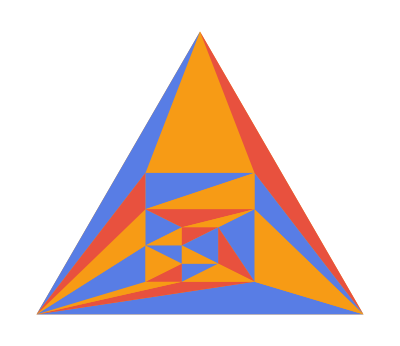

```mathematica
ResourceFunction[CloudObject["https://www.wolframcloud.com/obj/burbery1/DeployedResources/Function/ColorPlanarGraphFaces"]][GraphData[{"ChromaticallyEquivalent",{16,6,1}}]]
```

I can compare the number of vertices n with the number of edges which should be 3n-6.

```mathematica
AllTrue[triangulatedGraphsWithAtLastThreeVertices,3VertexCount[GraphData[#]]-6==EdgeCount[GraphData[#]]&]
```

True

This is true for all graphs.

## Exercise 47

Prove that the complete bigraph K_(3,3) isn’t planar.

This is related to the famous three utilities problem. It is well-known that you connect three houses to each other so each one has water, gas, and electricity. This means the complete bipartite graph K_(3,3) is not planar and cannot be embedded in the plane. This graph can however, be embedded on a torus. The toroidal embedding of this graph could be used to create a solution to the three utilities on a torus or donut or coffee cup or tire or other object that topologically homeomorphic to a torus.

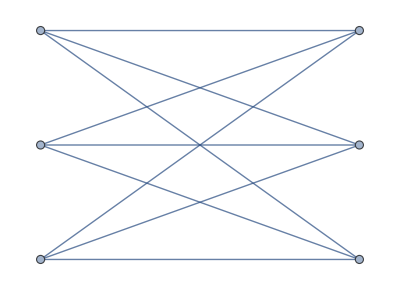

```mathematica
CompleteGraph[{3,3}]
```

```mathematica
PlanarGraphQ[CompleteGraph[{3,3}]]
```

False

Find the canonical graph:

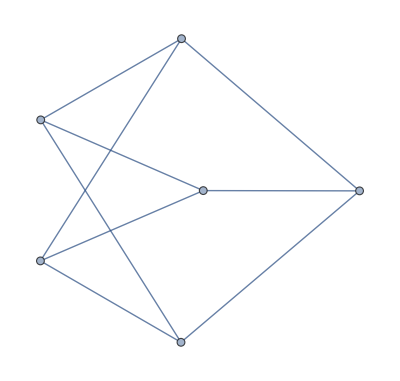

```mathematica
CanonicalGraph[CompleteGraph[{3,3}]]
```

Find the name of the graph data entry:

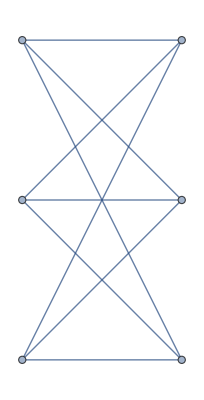

```mathematica
GraphData[{"CompleteBipartite", {3, 3}}]
```

Verify the graphs are isomorphic:

```mathematica
IsomorphicGraphQ[GraphData[{"CompleteBipartite", {3, 3}}],CompleteGraph[{3,3}]]
```

True

```mathematica
GraphData[{"CompleteBipartite",{3,3}},"Planar"]
```

False

The property apices is the list of vertices whose removal renders the graph planar:

```mathematica
GraphData[{"CompleteBipartite",{3,3}},"Apices"]
```

{1,2,3,4,5,6}

## Exercise 48

Complete the proof of Theorem B by showing that the stated procedure never the same color to two adjacent vertices.

Theorem B: A graph is bipartite if and only if it contains no cycle of odd length.

Conversely, if a graph contains no odd cycles we can color its vertices with the two colors {0,1} by carrying out the following procedure: Begin with all vertices uncolored. If all neighbors of colored vertices are already colored, choose an uncolored vertex w, and color it 0. Otherwise choose a colored vertex u that has an uncolored neighbor v; assign to v the opposite color. Exercise 48 proves that a valid 2-coloring is eventually obtained.

I will use examples to demonstrate a case for this.

```mathematica
GraphData["Bipartite"]
```

I will verify that all bipartite graphs have a chromatic number of two.

```mathematica
AllTrue[GraphData["Bipartite"],GraphData[#,"ChromaticNumber"]==2&]
```

False

I can color the vertices of a random sample of bipartite graphs:

```mathematica
RandomSample[GraphData["Bipartite"],30]
```

{Foster674A,{KayakPaddle,{4,8,2}},{Antelope,{8,8}},{Tree,{12,295}},{Giraffe,{8,10}},{Gear,16},Foster554A,3P3,{FibonacciCube,13},{Tree,{12,164}},2P2+K1,{Tree,{11,84}},{Path,10},{CompleteBipartite,{6,20}},{CubicTransitive,68},{CompleteBipartite,{8,9}},{HexagonalGrid,{1,1,3}},{Firecracker,{7,3}},{Tree,{11,187}},Foster936A,{CompleteBipartite,{13,19}},{MongolianTent,{2,5}},{CompleteBipartite,{9,20}},{EdgeTransitive,{18,3}},{Tree,{11,58}},{Camel,{6,10}},{GeneralizedPetersen,{24,11}},Foster194A,{Tree,{10,64}},Foster880A}

```mathematica
PersistResourceFunction["ColorGraphVertices"]
```

Success[…]

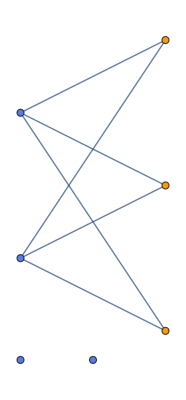
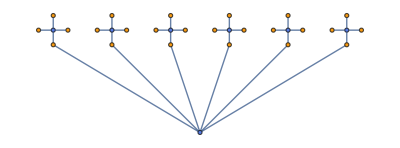
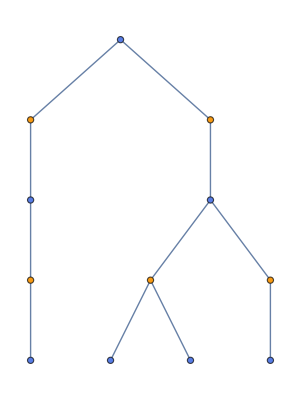
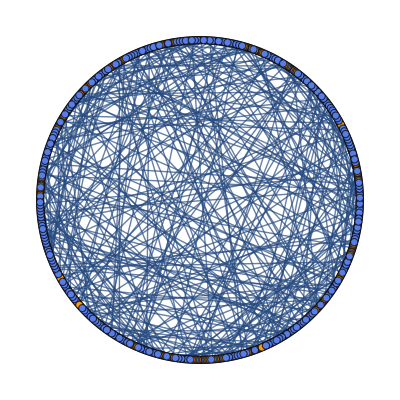
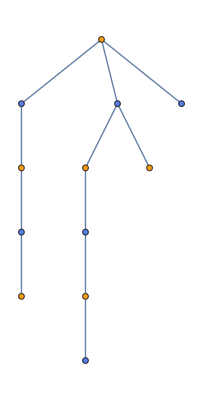
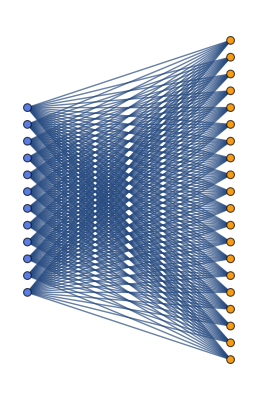
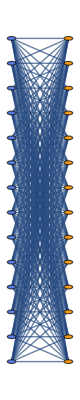
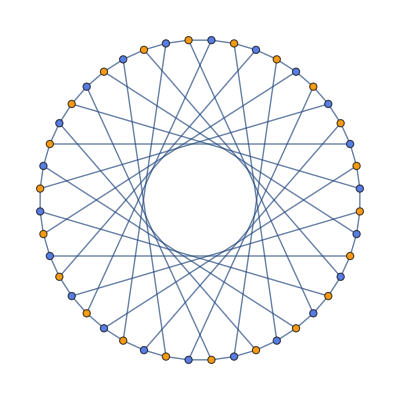

```mathematica
Select[GraphQ][ColorGraphVertices[GraphData[#]]&/@RandomSample[GraphData["Bipartite"],30]]
```

## Exercise 49

Draw diagrams of all the cubic graphs with at most 6 vertices:

```mathematica
GraphData["Cubic"]
```

```mathematica
Select[VertexCount[GraphData[#]]<=6&][GraphData["Cubic"]]
```

{{Prism,3},TetrahedralGraph,UtilityGraph}

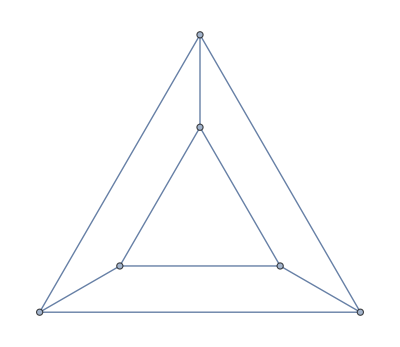
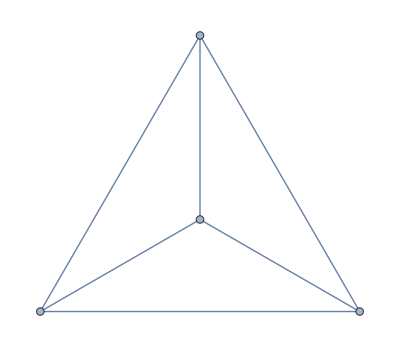
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphData/@Select[VertexCount[GraphData[#]]<=6&][GraphData["Cubic"]]
```

## Exercise 50

Find all bipartite graphs that can be 3-colored in exactly 24 ways.

```mathematica
GraphData["Bipartite"]
```

```mathematica
First[GraphData["Bipartite"]]
```

{6,13}

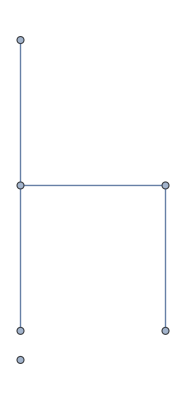

```mathematica
GraphData[First[GraphData["Bipartite"]]]
```

```mathematica
GraphData[First[GraphData["Bipartite"]],"ChromaticInvariant"]
```

0

```mathematica
GraphData[First[GraphData["Bipartite"]],"ChromaticNumber"]
```

2

```mathematica
GraphData[First[GraphData["Bipartite"]],"ChromaticPolynomial"]
```

(-1+#1)^4 #1^2&

```mathematica
GraphData[First[GraphData["Bipartite"]],"Chromatic"]
```

```mathematica
GraphData["ChromaticallyUnique"]
```

{{5,31},{6,66},{6,73},{6,80},{6,82},{6,97},{6,103},{6,109},{6,114},{6,124},{6,138},{6,148},{6,149},{7,129},{7,142},{7,151},{7,161},{7,169},{7,173},{7,179},{7,181},{7,210},{7,222},{7,254},{7,261},{7,266},{7,275},{7,288},{7,290},{7,302},{7,304},{7,316},{7,326},{7,328},{7,335},{7,337},{7,339},{7,344},{7,404},{7,477},{7,478},{7,503},{7,524},{7,574},{7,580},{7,582},{7,584},{7,585},{7,586},{7,622},{7,624},{7,645},{7,647},{7,674},{7,695},{7,696},{7,701},{7,708},{7,726},{7,730},{7,733},{7,748},{7,755},{7,763},{7,766},{7,771},{7,786},{7,789},{7,816},{7,832},{7,839},{7,840},{7,848},{7,849},{7,850},{7,858},{7,865},{7,868},{7,885},{7,886},{7,888},{7,896},{7,900},{7,901},{7,905},{7,906},{7,910},{7,937},{7,945},{7,957},{7,961},{7,962},{7,963},{7,964},{7,979},{7,1000},{7,1003},{7,1007},{7,1008},{7,1013},{7,1018},{7,1027},{7,1029},{7,1033},{7,1034},{7,1035},{7,1039},{7,1040},{8,579},{8,611},{8,628},{8,2989},{8,3914},{8,3921},{8,5516},{8,5519},{8,6777},{8,8186},{8,8953},{8,9760},{8,9880},{8,10354},{8,11242},{8,11481},{8,11486},{8,11504},{8,11566},{8,11585},{8,11690},{8,12265},{8,12333},{9,71752},{9,111589},{9,115869},{9,122423},{9,172352},{9,176255},{9,179236},{9,179238},{9,181483},{9,181502},{Antiprism,4},{Antiprism,5},BannerGraph,{Bar,{3,3}},{BiggestLittlePolygon,6},C3+2K1,C3+3K1,C3+4K1,C3+5K1,C3+K1,C4+2K1,C4+3K1,C4+K1,C5+2K1,C5+3K1,C5+K1,C6+K1,C7+K1,C8+K1,{Circulant,{7,{1,2}}},{Circulant,{8,{1,2,4}}},{Circulant,{9,{1,2}}},{Circulant,{9,{1,3}}},{Circulant,{9,{1,2,3}}},{Circulant,{10,{1,4}}},{Circulant,{10,{1,2,3}}},{Circulant,{10,{1,2,4}}},{Circulant,{10,{1,2,5}}},{Circulant,{10,{1,4,5}}},{Circulant,{10,{1,2,3,5}}},{Circulant,{10,{1,2,4,5}}},{CocktailParty,5},{CocktailParty,6},{CocktailParty,7},{CocktailParty,8},{CocktailParty,9},{CocktailParty,10},{CocktailParty,11},{CocktailParty,12},{CocktailParty,13},{CocktailParty,14},{CocktailParty,15},{CocktailParty,16},{CocktailParty,17},{CocktailParty,18},{CocktailParty,19},{CocktailParty,20},{Complete,6},{Complete,7},{Complete,8},{Complete,9},{Complete,10},{Complete,11},{Complete,12},{Complete,13},{Complete,14},{Complete,15},{Complete,16},{Complete,17},{Complete,18},{Complete,19},{Complete,20},{Complete,21},{Complete,22},{Complete,23},{Complete,24},{Complete,25},{Complete,26},{Complete,27},{Complete,28},{Complete,29},{Complete,30},{CompleteBipartite,{2,3}},{CompleteBipartite,{2,4}},{CompleteBipartite,{2,5}},{CompleteBipartite,{2,6}},{CompleteBipartite,{2,7}},{CompleteBipartite,{2,8}},{CompleteBipartite,{3,4}},{CompleteBipartite,{3,5}},{CompleteBipartite,{3,6}},{CompleteBipartite,{3,7}},{CompleteBipartite,{4,4}},{CompleteBipartite,{4,5}},{CompleteBipartite,{4,6}},{CompleteBipartite,{5,5}},{CompleteBipartite,{5,6}},{CompleteBipartite,{6,6}},{CompleteBipartite,{6,7}},{CompleteBipartite,{7,7}},{CompleteBipartite,{7,8}},{CompleteBipartite,{8,8}},{CompleteBipartite,{8,9}},{CompleteBipartite,{9,9}},{CompleteBipartite,{9,10}},{CompleteBipartite,{10,10}},{CompleteBipartite,{11,11}},{CompleteBipartite,{12,12}},{CompleteBipartite,{13,13}},{CompleteBipartite,{14,14}},{CompleteBipartite,{15,15}},{CompleteBipartite,{16,16}},{CompleteBipartite,{17,17}},{CompleteBipartite,{18,18}},{CompleteBipartite,{19,19}},{CompleteBipartite,{20,20}},{CompleteKPartite,{1,2,2,2}},{CompleteKPartite,{2,2,2,3}},{CompleteKPartite,{2,2,3,3}},{CompleteKPartite,{3,3,3,3}},{CompleteKPartite,{4,4,4,4}},{CompleteKPartite,{1,1,1,1,2}},{CompleteKPartite,{1,1,1,2,2}},{CompleteKPartite,{1,1,2,2,2}},{CompleteKPartite,{1,2,2,2,2}},{CompleteKPartite,{3,3,3,3,3}},{CompleteKPartite,{1,1,1,1,1,2}},{CompleteKPartite,{1,1,1,1,2,2}},{CompleteKPartite,{1,1,1,2,2,2}},{CompleteKPartite,{1,1,2,2,2,2}},{CompleteKPartite,{1,1,1,1,1,1,2}},{CompleteKPartite,{1,1,1,1,1,2,2}},{CompleteKPartite,{1,1,1,1,2,2,2}},{CompleteKPartite,{1,1,1,1,1,1,1,2}},{CompleteKPartite,{1,1,1,1,1,1,2,2}},{CompleteKPartite,{1,1,1,1,1,1,1,1,2}},{CompleteTripartite,{2,2,3}},{CompleteTripartite,{2,2,4}},{CompleteTripartite,{2,2,5}},{CompleteTripartite,{2,2,6}},{CompleteTripartite,{2,3,3}},{CompleteTripartite,{2,3,4}},{CompleteTripartite,{2,3,5}},{CompleteTripartite,{2,4,4}},{CompleteTripartite,{3,3,3}},{CompleteTripartite,{3,3,4}},{CompleteTripartite,{3,4,4}},{CompleteTripartite,{4,4,4}},{CompleteTripartite,{4,4,5}},{CompleteTripartite,{4,5,5}},{CompleteTripartite,{5,5,5}},{CompleteTripartite,{6,6,6}},{Cone,{5,3}},{Cone,{5,4}},{Cone,{5,5}},{Cone,{6,3}},{Cone,{6,4}},{Cone,{7,3}},CrossingNumberGraph2B,{Crown,5},{Cubic,{8,3}},{Cubic,{10,8}},{Cubic,{10,9}},{Cubic,{10,10}},{Cubic,{10,11}},{Cubic,{10,13}},{Cubic,{10,16}},{Cubic,{10,18}},CubicalGraph,{Cycle,5},{Cycle,6},{Cycle,7},{Cycle,8},{Cycle,9},{Cycle,10},{Cycle,11},{Cycle,12},{Cycle,13},{Cycle,14},{Cycle,15},{Cycle,16},{Cycle,17},{Cycle,18},{Cycle,19},{Cycle,20},{Cycle,21},{Cycle,22},{Cycle,23},{Cycle,24},{Cycle,25},{Cycle,26},{Cycle,27},{Cycle,28},{Cycle,29},{Cycle,30},DiamondGraph,{Dipyramid,3},{Dipyramid,5},{Dipyramid,7},{Dipyramid,8},DominoGraph,{DoubleToroidal,{8,6}},{DoubleToroidal,{8,9}},{DoubleToroidal,{8,10}},{DoubleToroidal,{8,11}},{EdgeTransitive,{9,14}},{Empty,2},{Empty,3},{Empty,4},{Empty,5},{Empty,6},{Empty,7},{Empty,8},{Empty,9},{Empty,10},{Empty,11},{Empty,12},{Empty,13},{Empty,14},{Empty,15},{Empty,16},{Empty,17},{Empty,18},{Empty,19},{Empty,20},{Empty,21},{Empty,22},{Empty,23},{Empty,24},{Empty,25},{Empty,26},{Empty,27},{Empty,28},{Empty,29},{Empty,30},FritschGraph,{Gear,3},{Grid,{3,3}},{Halin,{10,5}},{Halin,{10,12}},{HamiltonLaceable,{6,1}},{HamiltonLaceable,{8,2}},{HamiltonLaceable,{8,3}},{HamiltonLaceable,{8,4}},{HamiltonLaceable,{8,5}},{HamiltonLaceable,{8,7}},{HamiltonLaceable,{8,8}},{HamiltonLaceable,{8,9}},{HamiltonLaceable,{8,10}},{Harary,{3,7}},{Harary,{3,9}},{Harary,{5,9}},HemicubicalGraph,{HexagonalGrid,{1,1,2}},HouseGraph,HouseXGraph,{Jahangir,{3,3}},{JohnsonSkeleton,8},{JohnsonSkeleton,10},{JohnsonSkeleton,17},{JohnsonSkeleton,62},{JohnsonSkeleton,63},{JohnsonSkeleton,84},K2,2,3+K1,K2,3+2K1,K2,3+K1,K2,4+K1,K3,3+K1,K4+2K1,K4+3K1,K4,4-e,K4,5-4K2,K4-e+2K1,K4-e+3K1,K4-e+K1,K4+K1,K5+2K1,K5+3K1,K5+K1,K6+K1,K7+K1,K8+K1,K9+K1,{KCyclic,{11,235}},{KCyclic,{11,239}},{KCyclic,{11,269}},{KCyclic,{11,275}},{KCyclic,{11,309}},{KCyclic,{11,310}},{KCyclic,{11,311}},{KCyclic,{11,333}},{KCyclic,{11,336}},{KleinBottleTriangulation,{9,1}},LemkeGraph,{Lollipop,{4,1}},{Lollipop,{5,1}},{Lollipop,{6,1}},{Lollipop,{7,1}},{Matchstick,{7,26}},{Matchstick,{7,55}},{Matchstick,{8,23}},{Matchstick,{8,75}},{Matchstick,{8,92}},{Matchstick,{8,165}},{Matchstick,{8,172}},{Matchstick,{9,87}},{Matchstick,{9,273}},{Matchstick,{9,287}},{Matchstick,{9,322}},{Matchstick,{9,437}},{Matchstick,{9,522}},{Matchstick,{9,543}},{Matchstick,{9,568}},{Matchstick,{10,53}},{Matchstick,{10,1507}},{MoebiusLadder,5},{MongolianTent,{3,3}},NechushtanGraph,OctahedralGraph,P2+2K1,P2+3K1,P2+4K1,P2+5K1,P2+K1,{Pan,5},{Pan,6},{Pan,7},{Pan,8},{Pan,9},PaschGraph,{Path,2},{Path,3},{PathComplement,6},{PathComplement,8},{PathComplement,10},PawGraph,PentagonalWedgeGraph,PentatopeGraph,PetersenGraph,{PlanarNonbipartiteOddShortestPathCount,{8,1}},{PlanarNonbipartiteOddShortestPathCount,{9,2}},{PlanarNonbipartiteOddShortestPathCount,{10,1}},{PlanarNonbipartiteOddShortestPathCount,{10,3}},{Prism,3},{Prism,5},{ProjectivePlanarForbidden,11},{ProjectivePlanarForbidden,12},{ProjectivePlanarForbidden,13},{ProjectivePlanarForbidden,15},{ProjectivePlanarForbidden,16},{ProjectivePlanarForbidden,17},{ProjectivePlanarForbidden,19},{ProjectivePlanarForbidden,20},{ProjectivePlanarForbidden,21},{ProjectivePlanarForbidden,28},{ProjectivePlanarForbidden,29},{ProjectivePlanarForbidden,31},{ProjectivePlanarForbidden,33},{ProjectivePlanarForbidden,34},{Quartic,{8,1}},{Quartic,{8,4}},{Quartic,{8,5}},{Quartic,{9,5}},{Quartic,{9,7}},{Quartic,{9,8}},{Quartic,{9,9}},{Quartic,{9,10}},{Quartic,{9,12}},{Quartic,{9,13}},{Quartic,{9,15}},{Quartic,{10,6}},{Quartic,{10,8}},{Quartic,{10,9}},{Quartic,{10,10}},{Quartic,{10,11}},{Quartic,{10,16}},{Quartic,{10,20}},{Quartic,{10,21}},{Quartic,{10,24}},{Quartic,{10,25}},{Quartic,{10,26}},{Quartic,{10,30}},{Quartic,{10,31}},{Quartic,{10,32}},{Quartic,{10,33}},{Quartic,{10,34}},{Quartic,{10,35}},{Quartic,{10,37}},{Quartic,{10,38}},{Quartic,{10,39}},{Quartic,{10,40}},{Quartic,{10,41}},{Quartic,{10,42}},{Quartic,{10,45}},{Quartic,{10,46}},{Quartic,{10,47}},{Quartic,{10,49}},{Quartic,{10,50}},{Quartic,{10,51}},{Quartic,{10,52}},{Quartic,{10,53}},{Quartic,{10,54}},{Quartic,{10,55}},{Quartic,{10,56}},{Quartic,{10,57}},{QuasiCubic,{9,2}},{QuasiCubic,{9,4}},{QuasiCubic,{9,5}},{QuasiCubic,{9,6}},{QuasiCubic,{9,12}},{QuasiCubic,{9,14}},{QuasiCubic,{9,19}},{QuasiCubic,{9,22}},{QuasiCubic,{9,23}},{QuasiCubic,{9,24}},{QuasiCubic,{9,27}},{QuasiQuintic,{9,5}},{QuasiQuintic,{9,6}},{QuasiQuintic,{9,7}},{QuasiQuintic,{9,12}},{QuasiQuintic,{9,17}},{QuasiQuintic,{9,18}},{QuasiQuintic,{9,19}},{Queen,{2,3}},{Quintic,{10,4}},{Quintic,{10,5}},{Quintic,{10,8}},{Quintic,{10,12}},{Quintic,{10,14}},{Quintic,{10,15}},{Quintic,{10,16}},{Quintic,{10,17}},{Quintic,{10,19}},{Quintic,{10,20}},{Quintic,{10,21}},{Quintic,{10,25}},{Quintic,{10,26}},{Quintic,{10,28}},{Quintic,{10,29}},{Quintic,{10,30}},{Quintic,{10,32}},{Quintic,{10,33}},{Quintic,{10,34}},{Quintic,{10,35}},{Quintic,{10,36}},{Quintic,{10,37}},{Quintic,{10,38}},{Quintic,{10,39}},{Quintic,{10,41}},{Quintic,{10,42}},{Quintic,{10,43}},{Quintic,{10,44}},{Quintic,{10,45}},{Quintic,{10,46}},{Quintic,{10,47}},{Quintic,{10,48}},{Quintic,{10,49}},{Quintic,{10,51}},{Quintic,{10,52}},{Quintic,{10,53}},{Quintic,{10,54}},{Quintic,{10,55}},{Quintic,{10,56}},{Quintic,{10,57}},{Quintic,{10,58}},{Rook,{2,5}},RoyleGraph1,RoyleGraph2,{SelfComplementary,{9,14}},{SelfDual,{7,6}},{SelfDual,{9,34}},{SelfDual,{9,41}},{SelfDual,{9,48}},{Septic,{10,4}},{Sextic,{10,2}},{Sextic,{10,3}},{Sextic,{10,4}},{Sextic,{10,6}},{Sextic,{10,9}},{Sextic,{10,10}},{Sextic,{10,11}},{Sextic,{10,12}},{Sextic,{10,13}},{Sextic,{10,14}},{Sextic,{10,15}},{Sextic,{10,16}},{Sextic,{10,17}},{Sextic,{10,21}},SingletonGraph,SixteenCellGraph,SoiferGraph,SquareGraph,TetrahedralGraph,ThetaZeroGraph,{Trapezohedron,4},TriangleGraph,{Triangular,5},{TriangularHoneycombQueen,4},{UnitDistanceForbidden,{6,9,1}},{UnitDistanceForbidden,{7,10,1}},{UnitDistanceForbidden,{7,11,1}},{UnitDistanceForbidden,{8,12,2}},{UnitDistanceForbidden,{8,13,1}},{UnitDistanceForbidden,{8,13,2}},{UnitDistanceForbidden,{8,13,8}},{UnitDistanceForbidden,{9,13,1}},{UnitDistanceForbidden,{9,13,2}},{UnitDistanceForbidden,{9,14,2}},{UnitDistanceForbidden,{9,14,6}},{UnitDistanceForbidden,{9,14,18}},{UnitDistanceForbidden,{9,14,19}},{UnitDistanceForbidden,{9,15,1}},{UnitDistanceForbidden,{9,15,2}},{UnitDistanceForbidden,{9,15,7}},{UnitDistanceForbidden,{9,15,10}},{UnitDistanceForbidden,{9,15,17}},{UnitDistanceForbidden,{9,15,20}},{UnitDistanceForbidden,{9,15,33}},UtilityGraph,W5+2K1,W5+K1,WagnerGraph,{Wheel,5},{Wheel,7},{Wheel,9},{Wheel,10},{WheelComplement,8},{WheelComplement,9},{WheelComplement,10},Y3+K1}

I wasn’t sure which GraphData property corresponded to the number of valid colorings for a graph, so I tried to find a pattern in some of the properties related to coloring, but couldn’t find a pattern.

```mathematica
First[GraphData["ChromaticallyUnique"]]
```

{5,31}

```mathematica
GraphData[First[GraphData["ChromaticallyUnique"]],"ChromaticPolynomial"]
```

(-2+#1) (-1+#1) #1 (5-4 #1+#1^2)&

```mathematica
GraphData[First[GraphData["ChromaticallyUnique"]],"QChromaticPolynomial"]
```

2+2/#1+#1&

I looked at the answer and one of them is the path graph 4.

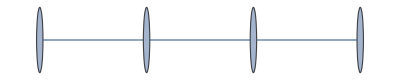

```mathematica
GraphData[{"Path", 4}]
```

I also tried to find a relationship between one of the color properties and 24, but couldn’t. As far as I know, GraphData does not include data on how many valid colorings there are of a graph. Please comment if you know the name of this property and if GraphData can compute it or if you can take the output of GraphData for a property and compute it.

```mathematica
GraphData[{"Path", 4},"ChromaticInvariant"]
```

0

```mathematica
GraphData[{"Path", 4},"ChromaticNumber"]
```

2

```mathematica
GraphData[{"Path", 4},"ChromaticPolynomial"][x]
```

(-1+x)^3 x

```mathematica
GraphData[{"Path", 4},"EdgeChromaticNumber"]
```

2

```mathematica
GraphData[{"Path", 4},"FractionalChromaticNumber"]
```

2

```mathematica
GraphData[{"Path", 4},"FractionalEdgeChromaticNumber"]
```

2

```mathematica
GraphData[{"Path", 4},"MinimumVertexColoring"]
```

{1,2,1,2}

```mathematica
GraphData[{"Path", 4},"MinimumEdgeColoring"]
```

{1,2,1}

```mathematica
GraphData[{"Path", 4},"MinimumWeightFractionalColoring"]
```

{{{1,3},1},{{2,4},1}}

## Exercise 55

How many edges are there in the complete k-partite graph K_(n_1,n_2,…,n_k)?

I’m going to use FindSequenceFunction to find a pattern.

```mathematica
Table[EdgeCount[CompleteGraph[ConstantArray[2,i]]],{i,9}]
```

{1,4,12,24,40,60,84,112,144}

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[2,i]]],{i,9}]]
```

I have a holonomic difference root object.

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[2,i]]],{i,9}]][100]
```

19800

I have a different result for 3.

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[3,i]]],{i,10}]]
```

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[4,i]]],{i,10}]]
```

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[5,i]]],{i,10}]]
```

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[6,i]]],{i,10}]]
```

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[7,i]]],{i,10}]]
```

```mathematica
FindSequenceFunction[{24,54,96,150,216,294}]
```

6 (1+2 #1+#1^2)&

```mathematica
FindSequenceFunction[{24,54,96,150,216,294}][x]
```

6 (1+2 x+x^2)

```mathematica
Simplify[FindSequenceFunction[{24,54,96,150,216,294}][x]]
```

6 (1+x)^2

It seems like the edge count’s holonomic fourth term is given by 6(1+x)^2.

```mathematica
InputForm[]
```

DifferenceRoot[Function[{y, n}, {98*n + (1 - n)*y[n] + (-3 + n)*y[1 + n] == 0, y[1] == 21, y[2] == 49, y[3] == 147, 
   y[4] == 294}]]

```mathematica
First[InputForm[]]
```

```mathematica
First[First[InputForm[]]]
```

Function[{y,n},{98 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==21,y[2]==49,y[3]==147,y[4]==294}]

```mathematica
Last[First[First[InputForm[]]]]
```

{98 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==21,y[2]==49,y[3]==147,y[4]==294}

```mathematica
Rest[Last[First[First[InputForm[]]]]]
```

{y[1]==21,y[2]==49,y[3]==147,y[4]==294}

```mathematica
Last/@Rest[Last[First[First[InputForm[]]]]]
```

{21,49,147,294}

```mathematica
Table[Last/@Rest[Last[First[First[InputForm[FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[e,i]]],{i,10}]]]]]]],{e,2,7}]
```

{{1,4,12,24},{3,9,27,54},{6,16,48,96},{10,25,75,150},{15,36,108,216},{21,49,147,294}}

```mathematica
Transpose[Table[Last/@Rest[Last[First[First[InputForm[FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[e,i]]],{i,10}]]]]]]],{e,2,7}]]
```

{{1,3,6,10,15,21},{4,9,16,25,36,49},{12,27,48,75,108,147},{24,54,96,150,216,294}}

```mathematica
FindSequenceFunction/@Transpose[Table[Last/@Rest[Last[First[First[InputForm[FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[e,i]]],{i,10}]]]]]]],{e,2,7}]]
```

{1/2 #1 (1+#1)&,1+2 #1+#1^2&,3 (1+2 #1+#1^2)&,6 (1+2 #1+#1^2)&}

```mathematica
Last[First[First[InputForm[]]]]
```

{98 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==21,y[2]==49,y[3]==147,y[4]==294}

```mathematica
First[Last[First[First[InputForm[]]]]]
```

98 n+(1-n) y[n]+(-3+n) y[1+n]==0

```mathematica
First[First[Last[First[First[InputForm[]]]]]]
```

98 n+(1-n) y[n]+(-3+n) y[1+n]

```mathematica
First[First[First[Last[First[First[InputForm[]]]]]]]
```

98 n

```mathematica
First[First[First[First[Last[First[First[InputForm[]]]]]]]]
```

98

```mathematica
Table[First[First[First[First[Last[First[First[InputForm[FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[e,i]]],{i,10}]]]]]]]]]],{e,2,7}]
```

{8,18,32,50,72,98}

```mathematica
FindSequenceFunction[Table[First[First[First[First[Last[First[First[InputForm[FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[e,i]]],{i,10}]]]]]]]]]],{e,2,7}]]
```

2 (1+2 #1+#1^2)&

```mathematica
FindSequenceFunction[Table[First[First[First[First[Last[First[First[InputForm[FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[e,i]]],{i,10}]]]]]]]]]],{e,2,7}]][x]
```

2 (1+2 x+x^2)

```mathematica
Simplify[2 (1+2 x+x^2)]
```

2 (1+x)^2

I now have an expression to compute the holonomic difference root. I have 2(1+x)^2 for the term that in this case is 98n. I have the {1/2 #1 (1+#1)&,1+2 #1+#1^2&,3 (1+2 #1+#1^2)&,6 (1+2 #1+#1^2)&} for y[1], y[2], y[3], and y[4].

```mathematica
Function[{y,n},{98 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==21,y[2]==49,y[3]==147,y[4]==294}]
```

I will test my hypothesis by constructing a difference root. I first thought I got this wrong but I realized I started from 2 so I need to do 11-1=10.

```mathematica
2 (1+2 #1+#1^2)&[10]
```

242

```mathematica
{1/2 #1 (1+#1)&[10],1+2 #1+#1^2&[10],3 (1+2 #1+#1^2)&[10],6 (1+2 #1+#1^2)&[10]}
```

{55,121,363,726}

```mathematica
DifferenceRoot[Function[{y,n},{242n+(1-n)y[n]+(-3+n)y[1+n]==0,y[1]==55,y[2]==121,y[3]==363,y[4]==726}]]
```

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[11,i]]],{i,10}]]
```

```mathematica
DifferenceRoot[Function[{y,n},{242n+(1-n)y[n]+(-3+n)y[1+n]==0,y[1]==55,y[2]==121,y[3]==363,y[4]==726}]]==FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[11,i]]],{i,10}]]
```

True

I can now construct a function to find the number of edges in a complete kpartite graph.

I will symbolically find what happens when I subtract 1

```mathematica
2 (1+2 #1+#1^2)&[x-1]
```

2 (1+2 (-1+x)+(-1+x)^2)

```mathematica
2 (1+2 #1+#1^2)&[x-1]//Simplify
```

2 x^2

```mathematica
{1/2 #1 (1+#1)&[x-1],1+2 #1+#1^2&[x-1],3 (1+2 #1+#1^2)&[x-1],6 (1+2 #1+#1^2)&[x-1]}
```

{1/2 (-1+x) x,1+2 (-1+x)+(-1+x)^2,3 (1+2 (-1+x)+(-1+x)^2),6 (1+2 (-1+x)+(-1+x)^2)}

```mathematica
FullSimplify/@{1/2 #1 (1+#1)&[x-1],1+2 #1+#1^2&[x-1],3 (1+2 #1+#1^2)&[x-1],6 (1+2 #1+#1^2)&[x-1]}//TraditionalForm
```

{1/2 (x-1) x,x^2,3 x^2,6 x^2}

```mathematica
KPartiteEdgeFunctionBuilder//ClearAll
KPartiteEdgeFunctionBuilder[k_]:=DifferenceRoot[Function[{y,n},{2 k^2 n+(1-n)y[n]+(-3+n)y[1+n]==0,y[1]==1/2(k-1)k,y[2]==k^2,y[3]==3 k^2,y[4]==6 k^2}]]
```

I will now input a test of 17:

```mathematica
KPartiteEdgeFunctionBuilder[17]
```

I will compute the answer manually:

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[17,i]]],{i,10}]]
```

```mathematica
KPartiteEdgeFunctionBuilder[17]==FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[17,i]]],{i,10}]]
```

True

I now have an answer to how many edges are in K_(n_1,…,n_k).

```mathematica
EdgesInCompleteKPartiteGraph//ClearAll
EdgesInCompleteKPartiteGraph[k_,n_]:=DifferenceRoot[Function[{y,n},{2 k^2 n+(1-n)y[n]+(-3+n)y[1+n]==0,y[1]==1/2(k-1)k,y[2]==k^2,y[3]==3 k^2,y[4]==6 k^2}]][n]
```

I can now quickly find how many edges are the graph K_(19_1,…,19_7).

```mathematica
EdgesInCompleteKPartiteGraph[7,19]
```

8379

I can check the answer

```mathematica
KPartiteEdgeFunctionBuilder[7][19]
```

8379

```mathematica
FindSequenceFunction[Table[EdgeCount[CompleteGraph[ConstantArray[7,i]]],{i,10}]][19]
```

8379

I am now going to look at the solution.

Donald Knuth has this answer:

(N
2)-(n_1
2)-…-(n_k
2), or (N^2-n_1^2-…-n_k^2)/2 where N=n_1+…+n_k.

I’m interested in there’s a way to transform my complicated holonomic differential root object into this simpler form. Maybe in future versions of Mathematica this can be done with some simplifications similar to how Mathematica has been able to find more closed form solutions for integrals over time. Please comment if you have any ideas on how to find the simpler result from the answers to the exercises. I would like to mention this is difficult because the term is multivariable.

I would like to mention that technically not even my complicated function is correct because the solution Knuth gives holds for when n_1≠n_2, for example, but in my case all n_i have to be the same where I used ConstantArray.

## Note

A lot of the exercises are hard and involve proofs and higher mathematical thinking as can be seen in my difficulty with the previous problem with holonomic difference root objects and bipartite graphs, so I’m going to skip to the exercises I can use Mathematica on.

## Exercise 83

Draw the graph OverBar[L(K_5)].

This is the graph complement of the line graph of the complete graph of 5.

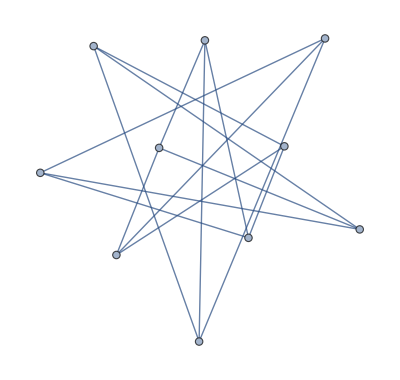

```mathematica
GraphComplement[LineGraph[CompleteGraph[5]]]
```

Transform the graph into a simpler form:

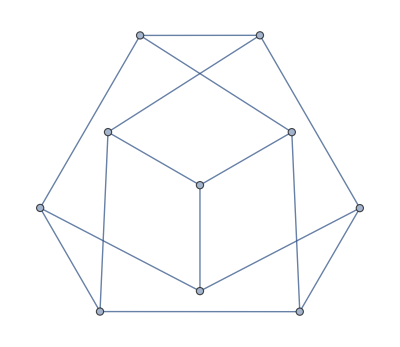

```mathematica
CanonicalGraph[GraphComplement[LineGraph[CompleteGraph[5]]]]
```

I think this is isomorphic to the Petersen graph.

```mathematica
IsomorphicGraphQ[CanonicalGraph[GraphComplement[LineGraph[CompleteGraph[5]]]],PetersenGraph[]]
```

True

I learned  OverBar[L(K_5)] equals the Petersen graph.

## Exercise 84

Is L(K_(3,3)) self-complementary?

Find all known self-complementary graphs:

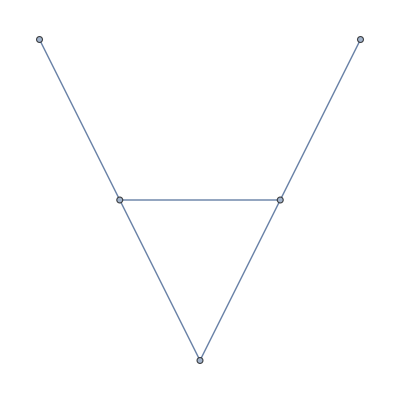
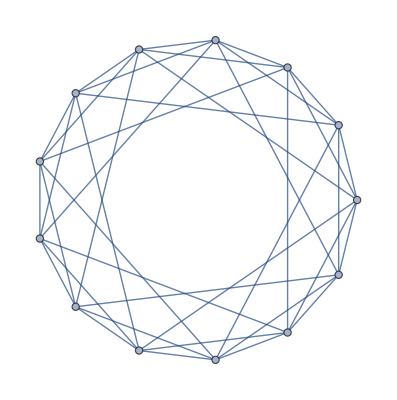
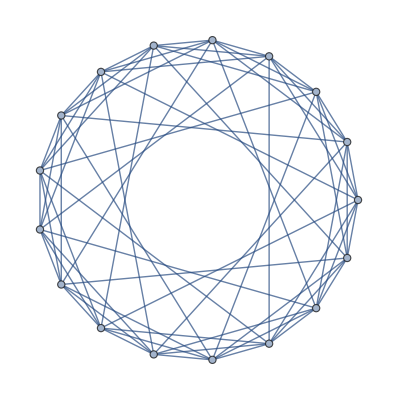
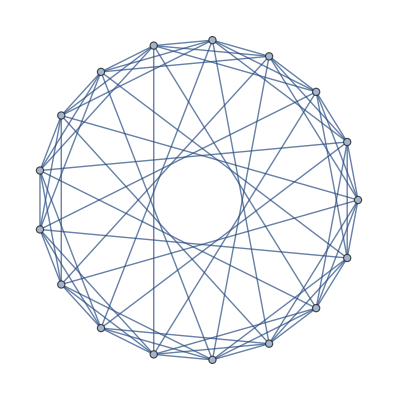
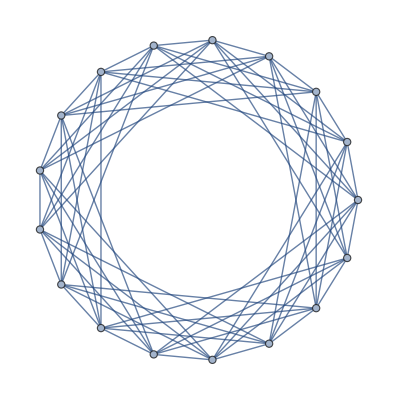
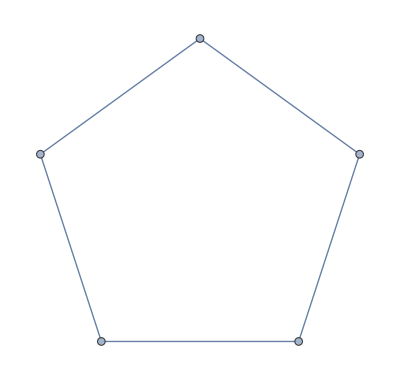
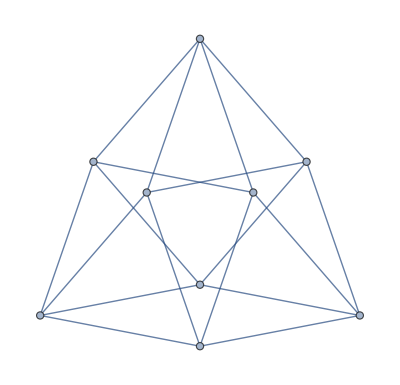
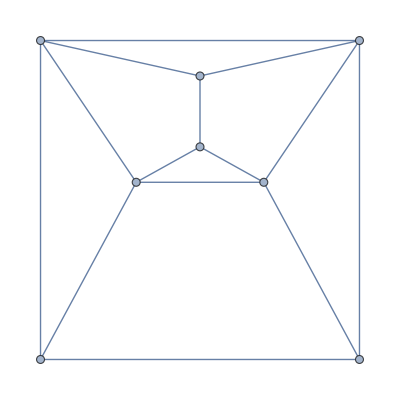
<|BullGraph→-Graphics-,{Circulant,{13,{1,2,4}}}→-Graphics-,{Circulant,{17,{1,2,3,6}}}→-Graphics-,{Circulant,{17,{1,2,3,7}}}→-Graphics-,{Circulant,{17,{1,3,4,5}}}→-Graphics-,{Cycle,5}→-Graphics-,{GeneralizedQuadrangle,{2,1}}→-Graphics-,{JohnsonSkeleton,26}→-Graphics-,{Paley,13}→-Graphics-,{Paley,17}→-Graphics-,{Paley,25}→-Graphics-,{Paley,29}→-Graphics-,{Paley,37}→-Graphics-,{Paley,41}→-Graphics-,{Paley,49}→-Graphics-,{Paley,53}→-Graphics-,{Paley,61}→-Graphics-,{Paley,73}→-Graphics-,{Paley,81}→-Graphics-,{Paley,89}→-Graphics-,{Paley,97}→-Graphics-,{Paley,101}→-Graphics-,{Paley,109}→-Graphics-,{Paley,113}→-Graphics-,{Paley,121}→-Graphics-,{Paley,125}→-Graphics-,{Paley,137}→-Graphics-,{Paley,149}→-Graphics-,{Paley,157}→-Graphics-,{Paley,169}→-Graphics-,{Path,4}→-Graphics-,{Quartic,{9,2}}→-Graphics-,{Quartic,{9,8}}→-Graphics-,{Quartic,{9,11}}→-Graphics-,{SelfComplementary,{8,1}}→-Graphics-,{SelfComplementary,{8,3}}→-Graphics-,{SelfComplementary,{8,4}}→-Graphics-,{SelfComplementary,{8,5}}→-Graphics-,{SelfComplementary,{8,6}}→-Graphics-,{SelfComplementary,{8,7}}→-Graphics-,{SelfComplementary,{8,8}}→-Graphics-,{SelfComplementary,{8,10}}→-Graphics-,{SelfComplementary,{9,1}}→-Graphics-,{SelfComplementary,{9,2}}→-Graphics-,{SelfComplementary,{9,3}}→-Graphics-,{SelfComplementary,{9,4}}→-Graphics-,{SelfComplementary,{9,5}}→-Graphics-,{SelfComplementary,{9,6}}→-Graphics-,{SelfComplementary,{9,7}}→-Graphics-,{SelfComplementary,{9,8}}→-Graphics-,{SelfComplementary,{9,9}}→-Graphics-,{SelfComplementary,{9,10}}→-Graphics-,{SelfComplementary,{9,11}}→-Graphics-,{SelfComplementary,{9,12}}→-Graphics-,{SelfComplementary,{9,13}}→-Graphics-,{SelfComplementary,{9,14}}→-Graphics-,{SelfComplementary,{9,15}}→-Graphics-,{SelfComplementary,{9,16}}→-Graphics-,{SelfComplementary,{9,17}}→-Graphics-,{SelfComplementary,{9,18}}→-Graphics-,{SelfComplementary,{9,19}}→-Graphics-,{SelfComplementary,{9,20}}→-Graphics-,{SelfComplementary,{9,21}}→-Graphics-,{SelfComplementary,{9,22}}→-Graphics-,{SelfComplementary,{9,23}}→-Graphics-,{SelfComplementary,{9,26}}→-Graphics-,{SelfComplementary,{9,27}}→-Graphics-,{SelfComplementary,{9,28}}→-Graphics-,{SelfComplementary,{9,29}}→-Graphics-,{SelfComplementary,{9,30}}→-Graphics-,{SelfComplementary,{9,31}}→-Graphics-,{SelfComplementary,{9,32}}→-Graphics-,{SelfComplementary,{9,34}}→-Graphics-,{SelfComplementary,{9,35}}→-Graphics-,SingletonGraph→-Graphics-,{Sun,4}→-Graphics-|>

```mathematica
AssociationMap[GraphData,GraphData["SelfComplementary"]]
```

```mathematica
SelfComplementaryGraphQ//ClearAll
SelfComplementaryGraphQ[graph_?GraphQ]:=IsomorphicGraphQ[graph,GraphComplement[graph]]
```

```mathematica
SelfComplementaryGraphQ[LineGraph[CompleteGraph[{3,3}]]]
```

True

```mathematica
LineGraph[CompleteGraph[{3,3}]]
```

-Graphics-

```mathematica
GraphComplement[LineGraph[CompleteGraph[{3,3}]]]
```

-Graphics-

```mathematica
IsomorphicGraphQ[GraphComplement[LineGraph[CompleteGraph[{3,3}]]],LineGraph[CompleteGraph[{3,3}]]]
```

True

The answer is that L(K_(3,3)) is self-complementary.

The book says the answer is true. I originally got this wrong because I compared the graph and its complement with == instead of IsomorphicGraphQ.

## Exercise 87

Is the Petersen graph (a) 3-colorable (b) 3-edge-colorable?

```mathematica
GraphData["PetersenGraph","ChromaticNumber"]
```

3

```mathematica
GraphData["PetersenGraph","EdgeChromaticNumber"]
```

4

Yes to a, no to b.

```mathematica
ColorGraphVertices[PetersenGraph[],ImageSize->Large,VertexSize->Large]
```

-Graphics-

```mathematica
PersistResourceFunction[{"ColorGraphEdges"}]
```

{Success[…]}

```mathematica
ColorGraphEdges[PetersenGraph[],ImageSize->Large,EdgeStyle->{Thick}]
```

-Graphics-

## Exercise 88

The graph W_n=K_1—C_n is called the wheel with n spokes, when n>=3. How many cycles does it contain as subgraphs?

```mathematica
WheelGraph/@Range[12]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FindFundamentalCycles[WheelGraph[7]]
```

{{7<->1,1<->6,6<->7},{6<->1,1<->5,5<->6},{5<->1,1<->4,4<->5},{4<->1,1<->3,3<->4},{7<->1,1<->2,2<->7},{3<->1,1<->2,2<->3}}

```mathematica
Length[FindFundamentalCycles[WheelGraph[7]]]
```

6

Find all cycles of wheel graph 7.

```mathematica
FindCycle[WheelGraph[7],Infinity,All]
```

{{1<->3,3<->4,4<->1},{1<->4,4<->5,5<->1},{2<->7,7<->1,1<->2},{2<->3,3<->1,1<->2},{1<->5,5<->6,6<->1},{1<->7,7<->6,6<->1},{1<->3,3<->2,2<->7,7<->1},{1<->3,3<->4,4<->5,5<->1},{5<->1,1<->7,7<->6,6<->5},{2<->3,3<->4,4<->1,1<->2},{1<->2,2<->7,7<->6,6<->1},{1<->4,4<->5,5<->6,6<->1},{1<->4,4<->3,3<->2,2<->7,7<->1},{5<->4,4<->1,1<->7,7<->6,6<->5},{2<->7,7<->6,6<->5,5<->1,1<->2},{2<->3,3<->4,4<->5,5<->1,1<->2},{1<->3,3<->2,2<->7,7<->6,6<->1},{1<->3,3<->4,4<->5,5<->6,6<->1},{1<->7,7<->2,2<->3,3<->4,4<->5,5<->1},{5<->1,1<->3,3<->2,2<->7,7<->6,6<->5},{5<->4,4<->3,3<->1,1<->7,7<->6,6<->5},{5<->4,4<->3,3<->2,2<->7,7<->6,6<->5},{2<->7,7<->6,6<->5,5<->4,4<->1,1<->2},{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1},{1<->4,4<->3,3<->2,2<->7,7<->6,6<->1},{5<->1,1<->4,4<->3,3<->2,2<->7,7<->6,6<->5},{5<->4,4<->1,1<->3,3<->2,2<->7,7<->6,6<->5},{2<->7,7<->6,6<->5,5<->4,4<->3,3<->1,1<->2},{2<->3,3<->4,4<->5,5<->6,6<->7,7<->1,1<->2},{1<->5,5<->4,4<->3,3<->2,2<->7,7<->6,6<->1},{1<->7,7<->2,2<->3,3<->4,4<->5,5<->6,6<->1}}

```mathematica
Length[FindCycle[WheelGraph[7],Infinity,All]]
```

31

```mathematica
Table[Length[FindCycle[WheelGraph[i],Infinity,All]],{i,3,18}]
```

{2,7,13,21,31,43,57,73,91,111,133,157,183,211,241,273}

```mathematica
FindSequenceFunction[Table[Length[FindCycle[WheelGraph[i],Infinity,All]],{i,3,18}]]
```

Donald Knuth doesn’t give a particular answer for this.

## Exercise 91

Draw diagrams for the 4-vertex graphs (a)K_2(□K)_2

The symbol □ represents the Cartesian graph product.

```mathematica
GraphProduct[CompleteGraph[2],CompleteGraph[2]]
```

-Graphics-

(b) K_2⊗K_2. The symbol ⊗ represents the juxtaposition, or direct sum of two graphs. I think I have the right function.

```mathematica
GraphDisjointUnion[CompleteGraph[2],CompleteGraph[2]]
```

-Graphics-

Later on the symbol ⊗ is also used for the conjunction or direct product. I’m not sure if this is implemented in Mathematica or not yet.

```mathematica
GraphProduct[CompleteGraph[2],CompleteGraph[2],"Conormal"]
```

-Graphics-

(c) K_2 symbol K_2. Mathematica doesn’t support the next symbol, which is like a square with an X through its center, similar to the tensor product symbol used in part b but with a square instead of a circle.

I’m going to move onto another exercise because I’m not sure which graph product to use.

## Exercise 124

What is the chromatic number of the Chvàtal graph, Fig. 2(f)?

```mathematica
GraphData["ChvatalGraph","ChromaticNumber"]
```

4

Color the nodes:

```mathematica
ColorGraphVertices[GraphData["ChvatalGraph"],ImageSize->Large,VertexSize->Large]
```

-Graphics-

## Exercise 129

Describe the maximal cliques of the 8x8 queen graph (37).

```mathematica
GraphData[{"Queen", {8, 8}}]
```

-Graphics-

```mathematica
GraphData[{"Queen", {8, 8}},"MaximumCliques"]
```

{{1,2,3,4,5,6,7,8},{1,9,17,25,33,41,49,57},{1,10,19,28,37,46,55,64},{2,10,18,26,34,42,50,58},{3,11,19,27,35,43,51,59},{4,12,20,28,36,44,52,60},{5,13,21,29,37,45,53,61},{6,14,22,30,38,46,54,62},{7,15,23,31,39,47,55,63},{8,15,22,29,36,43,50,57},{8,16,24,32,40,48,56,64},{9,10,11,12,13,14,15,16},{17,18,19,20,21,22,23,24},{25,26,27,28,29,30,31,32},{33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48},{49,50,51,52,53,54,55,56},{57,58,59,60,61,62,63,64}}

```mathematica
HighlightGraph[GraphData[{"Queen", {8, 8}}],#]&/@GraphData[{"Queen", {8, 8}},"MaximumCliques"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The book says 310 maximal cliques which is different from the answer from GraphData, so I’m confused.

## Exercise 130

How many maximal cliques are in a complete k-partite graph?

I will try FindSequenceFunction.

```mathematica
Names["*clique*",IgnoreCase->True]
```

{FindClique,FindKClique}

```mathematica
Information/@Names["*clique*",IgnoreCase->True]
```

{,}

```mathematica
CompleteGraph[#]&/@Range[9]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FindClique[CompleteGraph[5],Infinity,All]
```

{{1,2,3,4,5}}

```mathematica
FindClique[CompleteGraph[#],Infinity,All]&/@Range[7]
```

{{{1}},{{1,2}},{{1,2,3}},{{1,2,3,4}},{{1,2,3,4,5}},{{1,2,3,4,5,6}},{{1,2,3,4,5,6,7}}}

I looks like a complete graph has just one maximal clique.

## Exercise 132

I tried to finish entering a graph manually and it was taking too much time so I gave up.

There’s a picture of a graph and I’m asked to determine several properties.

I was trying to be careful as I entered the graph into Mathematica not to duplicate an edge, but then I realized that if I duplicated an edge I could just use SimpleGraph to get the underlying graph.

```mathematica
SimpleGraph@Graph[{AA<->b,AA<->fSharp,AA<->cSharp,AA<->DD,AA<->EE,DD<->fSharp,DD<->b,DD<->e,DD<->GG,GG<->e,GG<->b,GG<->a,GG<->CC,CC<->e,CC<->a,CC<->d,CC<->FF,FF<->a,FF<->d,FF<->g,FF<->BFlat,BFlat<->d,BFlat<->c,BFlat<->g,BFlat<->EFlat,EFlat<->AFlat,EFlat<->f,EFlat<->c,EFlat<->g,AFlat<->c,AFlat<->f,AFlat<->BFlat,AFlat<->DFlat,DFlat<->f,DFlat<->bFlat,DFlat<->eFlat,DFlat<->GFlat,GFlat<->eFlat,GFlat<->bFlat,GFlat<->dFlat,GFlat<->BB,GFlat<->gSharp,BB<->EE,EE<->cSharp,EE<->fSharp,EE<->gSharp,gSharp<->BB,gSharp<->cSharp,cSharp<->fSharp,cSharp<->BB,AFlat<->DFlat,DFlat<->f},VertexLabels->Automatic,ImageSize->Large]
```

-Graphics-

```mathematica
SimpleGraphQ[SimpleGraph@Graph[{AA<->b,AA<->fSharp,AA<->cSharp,AA<->DD,AA<->EE,DD<->fSharp,DD<->b,DD<->e,DD<->GG,GG<->e,GG<->b,GG<->a,GG<->CC,CC<->e,CC<->a,CC<->d,CC<->FF,FF<->a,FF<->d,FF<->g,FF<->bFlat,bFlat<->d,bFlat<->c,bFlat<->g,bFlat<->eFlat,eFlat<->aFlat,eFlat<->f,eFlat<->c,eFlat<->g,aFlat<->c,aFlat<->f,aFlat<->bFlat,aFlat<->dFlat,dFlat<->f,dFlat<->bFlat,dFlat<->eFlat,dFlat<->gFlat,gFlat<->eFlat,gFlat<->bFlat,gFlat<->dFlat},VertexLabels->Automatic,GraphLayout->"TutteEmbedding"]]
```

True

### Order

## Conclusion

I was able to solve several exercises in TAOCP with Mathematica.